# Introduction

## Supply & Demand in the Short-run

```mathematica
x[α_,r_]:=α-r/2;
s[r_,αBar_]:=Integrate[1-x[α,r],{α,αBar,1}];
d[r_,αBar_]:=Integrate[x[α,r],{α,r/2,αBar}];
```

```mathematica
Manipulate[Plot[x[α,r],{α,0,1},
AxesOrigin->{0,0},
PlotRange->{-1,1},
Epilog->{Dashed,Line[{{r/2,0},{r/2,1}}]}],
{r,0,1},{p,0,1}]
```

## Market Clearing

```mathematica
sol=Solve[s[r,αBar]==d[r,αBar],r];
```

```mathematica
r1[p_]=(r/.sol[[1]])/.{αBar->Sqrt[p]};
r2[p_]=(r/.sol[[2]])/.{αBar->Sqrt[p]};
```

```mathematica
R[p_]:=Max[0,r1[p]];
S1[p_]=s[r1[p],Sqrt[p]]//FullSimplify;
D1[p_]=d[r1[p],Sqrt[p]]//FullSimplify;
```

## Selecting the corrent short-run rate

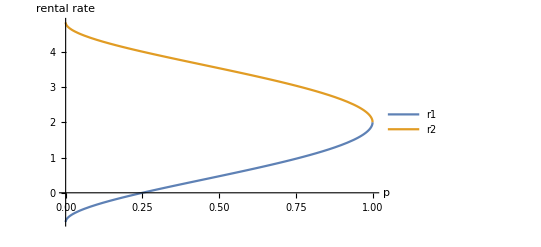

```mathematica
Plot[{r1[p],r2[p]},{p,0,1},PlotLegends->{"r1","r2"},AxesLabel->{"p","rental rate"}]
```

```mathematica
r1[p]
```

```mathematica
2 (1-√2 √(1-√p))//TeXForm
```

2 \left(1-\sqrt{2} \sqrt{1-\sqrt{p}}\right)

```mathematica
Manipulate[Plot[Max[0,x[α,r]]/.r->Max[0,r1[p]],{α,0,1},
AxesOrigin->{0,0},
PlotRange->{-.1,1},
AxesLabel->{"α, Valuation of Good","Amount Consumed"},
Epilog->{Dashed,
Line[{{r/2/.r->r1[p],0},{r/2/.r->r1[p],1}}],
Dotted,
Line[{{Sqrt[p],0},{Sqrt[p],1}}],
Text["Buy",{1/2+Sqrt[p]/2,0.8}],
Text["Rent",{((r/2 +Sqrt[p])/2)/.r->r1[p],0.8}],
Text["Does\nNot\nUse",{((0+r/2)/2)/.r->r1[p],0.70}]
}],
{{p,0.6},0,1}]
```

## Comparison of short-and long-run rental rates

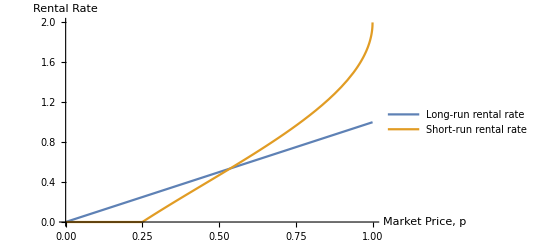

```mathematica
g=Plot[{p,R[p]},{p,0,1},PlotLegends->{"Long-run rental rate","Short-run rental rate"}, 
AxesLabel->{"Market Price, p","Rental Rate"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["../writeup/plots/cont_types.pdf", g]
```

../writeup/plots/cont_types.pdf

## When is there a glut?

If purchase price is sufficiently low (p < 1/4), there is a glut, at which point there rental rate is 0.

```mathematica
Solve[r1[p]==0,p]
```

{{p→1/4}}

## What is the quantity exchanged?

```mathematica
s[0,Sqrt[p]]
```

1/2-√p+p/2

```mathematica
S1[p_]=s[R[p],Sqrt[p]]//FullSimplify
```

1/2 (-1+√p) (-1+√p-Max[0,2-2 √(2-2 √p)])

```mathematica
r
```

```mathematica
Clear[r]
```

```mathematica
Integrate[x[α,r1[p]],{α,0,Sqrt[p]}]//FullSimplify
```

1/2 (-2+2 √(2-2 √p)+√p) √p

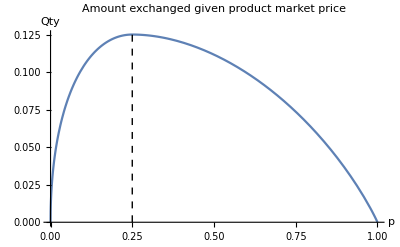

```mathematica
gQ=Plot[If[p > 1/4,S1[p],1/2 (-2+2 √(2-2 √p)+√p) √p],{p,0,1},PlotLabel->"Amount exchanged given product market price",
AxesOrigin->{0,0}, Epilog->{Dashed,Line[{{1/4,0},{1/4,1}}]},
AxesLabel->{"p","Qty"}]
```

```mathematica
Export["../writeup/plots/cont_qty.pdf", gQ]
```

../writeup/plots/cont_qty.pdf

```mathematica
S1[0]//N
```

0.0857864

```mathematica
x[α_,r_]:=α-r/2
```

```mathematica
s[r_,αBar_]:=Integrate[1-x[α,r],{α,αBar,1}];
d[r_,αBar_]:=Integrate[x[α,r],{α,r/2,αBar}];
```

```mathematica
sol=Solve[s[r,αBar]==d[r,αBar],r]
```

{{r→2 (1-√2 √(1-αBar))},{r→2 (1+√2 √(1-αBar))}}

## What is social welfare?

```mathematica
u[α_,r_]:=2*α*x[α,r]-x[α,r]^2-r*x[α,r]
```

```mathematica
u[α,r]/.r->r1[p]//FullSimplify
```

(-1+√(2-2 √p)+α)^2

```mathematica
u2[α_,r_]:=2*α*x[α,r]-x[α,r]^2+r*(1-x[α,r])
```

```mathematica
u2[α,r]/.r->r1[p]//FullSimplify
```

5-4 √(2-2 √p)-2 √p+α (-2+2 √(2-2 √p)+α)

```mathematica
r1[p]/2
```

1-√2 √(1-√p)

```mathematica
Integrate[(-1+√(2-2 √p)+α)^2,{α,1-√2 √(1-√p),Sqrt[p]}]//FullSimplify
```

```mathematica
1/3 (-1+√(2-2 √p)+√p)^3
```

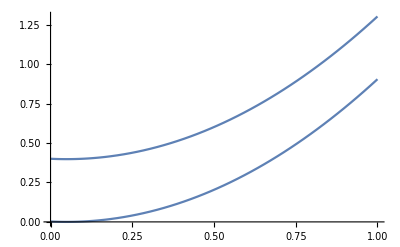

```mathematica
Plot[{(-1+√(2-2 √p)+α)^2,5-4 √(2-2 √p)-2 √p+α (-2+2 √(2-2 √p)+α)+p}/.p->0.3,{α,0,1}]
```

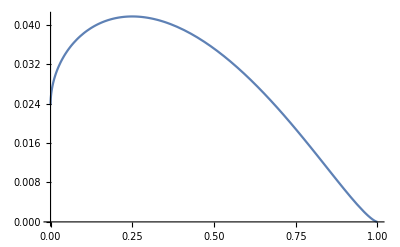

```mathematica
Plot[1/3 (-1+√(2-2 √p)+√p)^3,{p,0,1}]
```